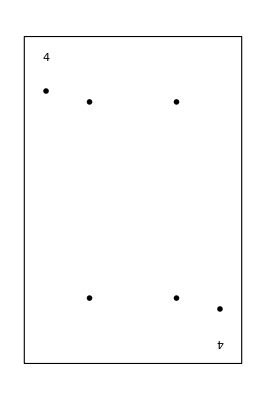
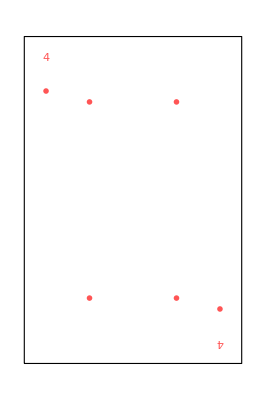
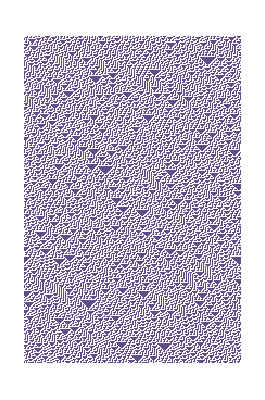
-Graphics--Graphics--Graphics--Graphics--Graphics-

-Graphics-

Inserisci la probabilità che si crei un tris con: 28 estraendo le carte rimanenti, per arrivare a 5, dal mazzo

Qual è la probabilità di fare un tris di 2 estraendo le prossime 2 carte dal mazzo?

```mathematica
SetDirectory[NotebookDirectory[]];
Get["randCard.nb"];
Get["calcolaProb.nb"];
(*
player=Input["Inserisci il numero di giocatori: "];
carteScoperte=Input["Inserisci il numero di carte scoperte: "];
*)
modalita=Input["Inserisci modalità"];
Switch[modalita,1,player=1;carteScoperte=4,
2,player=1;carteScoperte=3,
3,player=1;carteScoperte=3,
4,player=2;carteScoperte=3,
_, "Errore"];

(*CREO LE CARTE DEL BANCO E DEL GIOCATORE*)
{carteBanco,carteGiocatore}=randomCards[carteScoperte,player];

(*CREO IL DISEGNO DELLE CARTE AVVERSARIO*)
Switch[player,2,outputavversari=Row[{ImageResize[Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[3]],carteGiocatore[[4]]}],300]}],3,outputavversari=Row[{ImageResize[ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[3]],carteGiocatore[[4]]}],300],ImageResize[ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[5]],carteGiocatore[[6]]}],300]}],_,"Errore"];


(*CREO IL DISEGNO DELLE CARTE BANCO*)
outputbanco=Row[{ResourceFunction["PlayingCardGraphic"][carteBanco[[1]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[2]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[3]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[4]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[5]]]},Spacer[10]];
outputbanco;

(*CREO IL DISEGNO DELLE CARTE GIOCATORE*)
outputgiocatore=Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[1]],carteGiocatore[[2]]}];
outputgiocatore;


(*DISEGNO LE CARTE*)
If[player>1,Print[outputavversari]]
Print[outputbanco]
Print[outputgiocatore]



(*RICAVO LA PROBABILITA' CORRETTA E LA CARTA RICHIESTA*)
{correctprob, requestcard} = calcolaProb[carteBanco, carteGiocatore,player, modalita];

effectivecard = ToString[Mod[requestcard,13]];
Switch[effectivecard,
"11", effectivecard = "J",
"12", effectivecard = "Q",
"13", effectivecard = "K",
_, "Errore"];

Switch[modalita,
1,Print["Qual è la probabilità di fare una coppia di " <>effectivecard<> " estraendo la prossima carta dal mazzo?"],
2, Print["Qual è la probabilità di fare un tris di " <>effectivecard<> " estraendo le prossime 2 carte dal mazzo?"],
3, Print["Qual è la probabilità di fare una coppia di " <>effectivecard<> " estraendo le prossime 2 carte dal mazzo?"],
_, "Errore"]



(*CREO LA TEXTBOX E IL PULSANTE CHE VERIFICA IL RISULTATO AL SUO INTERNO*)
DynamicModule[{text="",result=""},answer=0;
Column[{InputField[Dynamic[text],String],Button["Verifica Risultato",answer=ToExpression[text];
result=checkAnswer[answer,correctprob,modalita];],Dynamic@Row[{result}]}]]
```